# Deriving fluid flow dynamics (different self-propulsion speed)

## Fluid flow (due to fish)

```mathematica
-Graphics-;
```

### FINITE-DIPOLE MODEL

Fish position vector :

```mathematica
OverBar[rf1]={xf1,yf1};
```

```mathematica
OverBar[rf2]={xf2,yf2};
```

Self-propulsion velocity DIFFERENT:

```mathematica
OverBar[vf1]=v01*{Cos[θf1],Sin[θf1]};
```

```mathematica
OverBar[vf2]=v02*{Cos[θf2],Sin[θf2]};
```

Some location:

```mathematica
r̄={x,y};
```

The potential field ϕ_fi (scalar) will be:

```mathematica
ϕf1=-r0^2*((r̄-OverBar[rf1]).OverBar[vf1])/((x-xf1)^2+(y-yf1)^2)
```

-(r0^2 (v01 (x-xf1) Cos[θf1]+v01 (y-yf1) Sin[θf1]))/((x-xf1)^2+(y-yf1)^2)

```mathematica
ϕf2=-r0^2*((r̄-OverBar[rf2]).OverBar[vf2])/((x-xf2)^2+(y-yf2)^2)
```

-(r0^2 (v02 (x-xf2) Cos[θf2]+v02 (y-yf2) Sin[θf2]))/((x-xf2)^2+(y-yf2)^2)

The velocity field ((ū)_fi=u_fi ī+v_fi j̄) is the gradient of the potential field:

```mathematica
OverBar[uf1]=Grad[ϕf1,{x,y}]//FullSimplify
```

{(r0^2 v01 ((x-xf1+y-yf1) (x-xf1-y+yf1) Cos[θf1]+2 (x-xf1) (y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2),(r0^2 v01 (2 (x-xf1) (y-yf1) Cos[θf1]-(x-xf1+y-yf1) (x-xf1-y+yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2)}

```mathematica
OverBar[uf2]=Grad[ϕf2,{x,y}]//FullSimplify
```

{(r0^2 v02 ((x-xf2+y-yf2) (x-xf2-y+yf2) Cos[θf2]+2 (x-xf2) (y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2),(r0^2 v02 (2 (x-xf2) (y-yf2) Cos[θf2]-(x-xf2+y-yf2) (x-xf2-y+yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)}

```mathematica
OverBar[uf]=OverBar[uf1]+OverBar[uf2] //FullSimplify
```

{r0^2 ((v01 ((x-xf1+y-yf1) (x-xf1-y+yf1) Cos[θf1]+2 (x-xf1) (y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2)+(v02 ((x-xf2+y-yf2) (x-xf2-y+yf2) Cos[θf2]+2 (x-xf2) (y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)),r0^2 ((v01 (2 (x-xf1) (y-yf1) Cos[θf1]-(x-xf1+y-yf1) (x-xf1-y+yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2)+(v02 (2 (x-xf2) (y-yf2) Cos[θf2]-(x-xf2+y-yf2) (x-xf2-y+yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))}

## Fluid flow (due to walls)

Method of images for influence of wall-bounded vorticity
Infinite number of image fish ( using  finite-dipole model)

```mathematica
-Graphics-;
```

Fish 1:

```mathematica
A1=((x-xf1)+I(y-yf1))/(2*h);  (*I=i=√(-1)*)
```

```mathematica
B1=((x-xf1)+I(y+yf1))/(2*h);
```

```mathematica
Ac1= ((x-xf1)-I(y-yf1))/(2*h)  (*complex conjugate of A*)
```

(x-xf1-ⅈ (y-yf1))/(2 h)

```mathematica
Bc1=((x-xf1)-I(y+yf1))/(2*h);  (*complex conjugate of B*)
```

Fish 2:

```mathematica
A2=((x-xf2)+I(y-yf2))/(2*h);  (*I=i=√(-1)*)
```

```mathematica
B2=((x-xf2)+I(y+yf2))/(2*h);
```

```mathematica
Ac2= ((x-xf2)-I(y-yf2))/(2*h);  (*complex conjugate of A*)
```

```mathematica
Bc2=((x-xf2)-I(y+yf2))/(2*h);  (*complex conjugate of B*)
```

Potential field (due to wall):

```mathematica
ϕw1=(r0^2*v01)/4*(4*((x-xf1)*Cos[θf1]+(y-yf1)*Sin[θf1])/((x-xf1)^2+(y-yf1)^2)-(π*ⅇ^(-ⅈ*θf1))/h*(ⅇ^(2*ⅈ*θf1)*((Coth[π*A1])+Coth[π*Bc1])+Coth[π*Ac1]+Coth[π*B1]));
```

```mathematica
ϕw2=(r0^2*v02)/4*(4*((x-xf2)*Cos[θf2]+(y-yf2)*Sin[θf2])/((x-xf2)^2+(y-yf2)^2)-(π*ⅇ^(-ⅈ*θf2))/h*(ⅇ^(2*ⅈ*θf2)*((Coth[π*A2])+Coth[π*Bc2])+Coth[π*Ac2]+Coth[π*B2]));
```

Velocity field (due to wall):

```mathematica
OverBar[uw1]=Grad[ϕw1,{x,y}];
```

```mathematica
OverBar[uw2]=Grad[ϕw2,{x,y}];
```

```mathematica
OverBar[uw]=OverBar[uw1]+OverBar[uw2]
```

{1/4 r0^2 v01 ((4 Cos[θf1])/((x-xf1)^2+(y-yf1)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+1/4 r0^2 v02 ((4 Cos[θf2])/((x-xf2)^2+(y-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)),1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((x-xf1)^2+(y-yf1)^2)-(8 (y-yf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((x-xf2)^2+(y-yf2)^2)-(8 (y-yf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))}

### Check

Verify that the walls of the channel are streamlines (sum of the velocity along y must be zero setting y=0 or y=h)

```mathematica
(*FullSimplify[Limit[(OverBar[uw][[2]]+OverBar[uf][[2]]),y->0],h>0]*)
```

```mathematica
(*FullSimplify[Limit[(OverBar[uw][[2]]+OverBar[uf][[2]]),y->h],h>0]*)
```

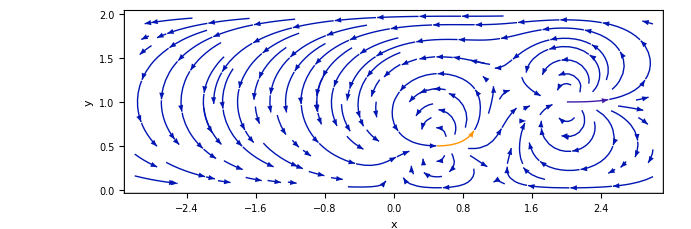

```mathematica
StreamPlot[(OverBar[uw]+OverBar[uf])/.{r0->1,v01->2,v02->2,h->2,θf1->0,θf2->0,xf2->0.5,yf2->0.5,xf1->2,yf1->1},{x,-3,3},{y,0,2},AspectRatio->1/3,FrameLabel->{"x","y"}]
```

## Background flow

Weakly rotational flow using ϵ: if ϵ→0 the background flow is irrotational

```mathematica
OverBar[ub]={U0*(1-4*ϵ*(y/h-1/2)^2),0}
```

{U0 (1-4 (-1/2+y/h)^2 ϵ),0}

## Overall fluid flow

The overall velocity field of the fluid flow in the channel at any point (x,y) is:

```mathematica
ū=OverBar[uf]+OverBar[uw]+OverBar[ub]
```

{U0 (1-4 (-1/2+y/h)^2 ϵ)+1/4 r0^2 v01 ((4 Cos[θf1])/((x-xf1)^2+(y-yf1)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+1/4 r0^2 v02 ((4 Cos[θf2])/((x-xf2)^2+(y-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))+r0^2 ((v01 ((x-xf1+y-yf1) (x-xf1-y+yf1) Cos[θf1]+2 (x-xf1) (y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2)+(v02 ((x-xf2+y-yf2) (x-xf2-y+yf2) Cos[θf2]+2 (x-xf2) (y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)),1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((x-xf1)^2+(y-yf1)^2)-(8 (y-yf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((x-xf2)^2+(y-yf2)^2)-(8 (y-yf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))+r0^2 ((v01 (2 (x-xf1) (y-yf1) Cos[θf1]-(x-xf1+y-yf1) (x-xf1-y+yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2)+(v02 (2 (x-xf2) (y-yf2) Cos[θf2]-(x-xf2+y-yf2) (x-xf2-y+yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))}

# Deriving fish dynamics

## Velocity

Advective velocity
Sum of the velocity due to the walls and the background flow in correspondence of the fish r̄=OverBar[r_fi]
OverBar[U_fi](OverBar[rfi],θ_fi)= (OverBar[u_w1](r̄,OverBar[r_f1],θ_f1)+OverBar[u_w2](r̄,OverBar[r_f2],θ_f2)+OverBar[u_b](r̄))+OverBar[u_fo](r̄,OverBar[r_fo],θ_fo)|_(r̄=OverBar[r_fi])

```mathematica
OverBar[ub[y_]]:={U0*(1-4*ϵ*(y/h-1/2)^2),0}
```

Advection fish 1  OverBar[U_f1]((r̄)_f1,θ_f1):

```mathematica
OverBar[uw11]=Limit[Limit[OverBar[uw1],y->yf1],x->xf1];
```

```mathematica
OverBar[uw21]=Limit[Limit[OverBar[uw2],y->yf1],x->xf1];
```

```mathematica
OverBar[uf21]=Limit[Limit[OverBar[uf2],y->yf1],x->xf1]; (*to run*)
```

```mathematica
OverBar[Uf1]=OverBar[uw11]+OverBar[uw21]+OverBar[ub[yf1]]+OverBar[uf21](*Advection Fish 1 also considering the effect of fish 2 as a finite-dipole*)
```

{U0 (1-4 (-1/2+yf1/h)^2 ϵ)-(ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) π^2 r0^2 v01 (1+3 Csc[(π yf1)/h]^2))/(24 h^2)+(r0^2 v02 ((xf1-xf2+yf1-yf2) (xf1-xf2-yf1+yf2) Cos[θf2]+2 (xf1-xf2) (yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)+1/4 r0^2 v02 ((4 Cos[θf2])/((xf1-xf2)^2+(yf1-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (xf1-xf2) ((xf1-xf2) Cos[θf2]+(yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)),(ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) π^2 r0^2 v01 (-1+3 Csc[(π yf1)/h]^2))/(24 h^2)+(r0^2 v02 (2 (xf1-xf2) (yf1-yf2) Cos[θf2]-(xf1-xf2+yf1-yf2) (xf1-xf2-yf1+yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((xf1-xf2)^2+(yf1-yf2)^2)-(8 (yf1-yf2) ((xf1-xf2) Cos[θf2]+(yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2))}

Advection fish 2  OverBar[U_f2]((r̄)_f2,θ_f2):

```mathematica
OverBar[uw12]=Limit[Limit[OverBar[uw1],y->yf2],x->xf2];
```

```mathematica
OverBar[uw22]=Limit[Limit[OverBar[uw2],y->yf2],x->xf2];
```

```mathematica
OverBar[uf12]=Limit[Limit[OverBar[uf1],y->yf2],x->xf2];
```

```mathematica
OverBar[Uf2]=OverBar[uw12]+OverBar[uw22]+OverBar[ub[yf2]]+OverBar[uf12]    (*Advection Fish 2*)
```

{U0 (1-4 (-1/2+yf2/h)^2 ϵ)-(ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) π^2 r0^2 v02 (1+3 Csc[(π yf2)/h]^2))/(24 h^2)+(r0^2 v01 ((-xf1+xf2+yf1-yf2) (-xf1+xf2-yf1+yf2) Cos[θf1]+2 (-xf1+xf2) (-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)+1/4 r0^2 v01 ((4 Cos[θf1])/((-xf1+xf2)^2+(-yf1+yf2)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (-xf1+xf2-ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (-xf1+xf2) ((-xf1+xf2) Cos[θf1]+(-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)),(ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) π^2 r0^2 v02 (-1+3 Csc[(π yf2)/h]^2))/(24 h^2)+(r0^2 v01 (2 (-xf1+xf2) (-yf1+yf2) Cos[θf1]-(-xf1+xf2+yf1-yf2) (-xf1+xf2-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)+1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (-xf1+xf2-ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((-xf1+xf2)^2+(-yf1+yf2)^2)-(8 (-yf1+yf2) ((-xf1+xf2) Cos[θf1]+(-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2))}

Thus, the fish velocity is given by:
OverDot[OverBar[r_fi]=]OverBar[U_fi](OverBar[rfi],θ_fi)+(v̄)_fi(θ_fi)       (I am calling OverDot[OverBar[r_fi]]  as OverBar[Vfi])

```mathematica
OverBar[rf1dot]=OverBar[Uf1]+OverBar[vf1]
```

{U0 (1-4 (-1/2+yf1/h)^2 ϵ)+v01 Cos[θf1]-(ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) π^2 r0^2 v01 (1+3 Csc[(π yf1)/h]^2))/(24 h^2)+(r0^2 v02 ((xf1-xf2+yf1-yf2) (xf1-xf2-yf1+yf2) Cos[θf2]+2 (xf1-xf2) (yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)+1/4 r0^2 v02 ((4 Cos[θf2])/((xf1-xf2)^2+(yf1-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (xf1-xf2) ((xf1-xf2) Cos[θf2]+(yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)),(ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) π^2 r0^2 v01 (-1+3 Csc[(π yf1)/h]^2))/(24 h^2)+v01 Sin[θf1]+(r0^2 v02 (2 (xf1-xf2) (yf1-yf2) Cos[θf2]-(xf1-xf2+yf1-yf2) (xf1-xf2-yf1+yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2)+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((xf1-xf2)^2+(yf1-yf2)^2)-(8 (yf1-yf2) ((xf1-xf2) Cos[θf2]+(yf1-yf2) Sin[θf2]))/(((xf1-xf2)^2+(yf1-yf2)^2)^2))}

```mathematica
OverBar[rf2dot]=OverBar[Uf2]+OverBar[vf2]
```

{U0 (1-4 (-1/2+yf2/h)^2 ϵ)+v02 Cos[θf2]-(ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) π^2 r0^2 v02 (1+3 Csc[(π yf2)/h]^2))/(24 h^2)+(r0^2 v01 ((-xf1+xf2+yf1-yf2) (-xf1+xf2-yf1+yf2) Cos[θf1]+2 (-xf1+xf2) (-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)+1/4 r0^2 v01 ((4 Cos[θf1])/((-xf1+xf2)^2+(-yf1+yf2)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (-xf1+xf2-ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (-xf1+xf2) ((-xf1+xf2) Cos[θf1]+(-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)),(ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) π^2 r0^2 v02 (-1+3 Csc[(π yf2)/h]^2))/(24 h^2)+(r0^2 v01 (2 (-xf1+xf2) (-yf1+yf2) Cos[θf1]-(-xf1+xf2+yf1-yf2) (-xf1+xf2-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2)+1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (-xf1+xf2-ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((-xf1+xf2)^2+(-yf1+yf2)^2)-(8 (-yf1+yf2) ((-xf1+xf2) Cos[θf1]+(-yf1+yf2) Sin[θf1]))/(((-xf1+xf2)^2+(-yf1+yf2)^2)^2))+v02 Sin[θf2]}

## Orientation

Hydrodynamic turn rate

```mathematica
(*GradU=Grad[OverBar[Unew],{x,y}]; *) (*gradient of the advective velocity*)
```

Fish 1:

```mathematica
OverBar[Unew1]=OverBar[uw]+OverBar[ub]+OverBar[uf2](*ADVECTION IN r*)
```

{U0 (1-4 (-1/2+y/h)^2 ϵ)+1/4 r0^2 v01 ((4 Cos[θf1])/((x-xf1)^2+(y-yf1)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+(r0^2 v02 ((x-xf2+y-yf2) (x-xf2-y+yf2) Cos[θf2]+2 (x-xf2) (y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)+1/4 r0^2 v02 ((4 Cos[θf2])/((x-xf2)^2+(y-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)),1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((x-xf1)^2+(y-yf1)^2)-(8 (y-yf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+(r0^2 v02 (2 (x-xf2) (y-yf2) Cos[θf2]-(x-xf2+y-yf2) (x-xf2-y+yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((x-xf2)^2+(y-yf2)^2)-(8 (y-yf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))}

```mathematica
(*GradU1=Limit[Limit[GradU,y->yf1],x->xf1] *)(*gradient of the advective velocity evaluated in rf1*)
```

```mathematica
(*Limit[Limit[{{D[OverBar[Unew][[1]],x],D[OverBar[Unew][[1]],y]},{D[OverBar[Unew][[2]],x],D[OverBar[Unew][[2]],y]}},y->yf1],x->xf1]*)
```

```mathematica
DUnew1x=Limit[Limit[D[OverBar[Unew1][[1]],x],y->yf1],x->xf1];
```

```mathematica
DUnew1y=Limit[Limit[D[OverBar[Unew1][[1]],y],y->yf1],x->xf1];
```

```mathematica
DUnew2x=Limit[Limit[D[OverBar[Unew1][[2]],x],y->yf1],x->xf1];
```

```mathematica
DUnew2y=Limit[Limit[D[OverBar[Unew1][[2]],y],y->yf1],x->xf1];
```

```mathematica
GradU1={{DUnew1x,DUnew1y},{DUnew2x,DUnew2y}};
```

```mathematica
OverVector[vf1]={Cos[θf1],Sin[θf1]}; (*unit vector*)
```

```mathematica
OverVector[vf1perp]={-Sin[θf1],Cos[θf1]};
```

```mathematica
Ω1=-OverVector[vf1].GradU1.OverVector[vf1perp]
```

Sin[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2-ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅈ ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2-Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])-Cos[θf1] (1/(8 h^3)Cos[θf1] (ⅇ^(-ⅈ θf1) (32 ⅇ^(ⅈ θf1) h^2 U0 ϵ-64 ⅇ^(ⅈ θf1) h U0 yf1 ϵ+π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(2 ⅈ θf1) π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2)-ⅈ ⅇ^(-ⅈ θf2) π^3 r0^2 v02 (-Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (-ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])

Hydrodynamic feedback(lateral line sensing):

Local fluid vorticity:

```mathematica
OverBar[ωb[y_]]:=(8*U0*ϵ)/h*(y/h-1/2);
```

```mathematica
λ1=K*r0*l*OverBar[ωb[yf1]]
```

(8 K l r0 U0 (-1/2+yf1/h) ϵ)/h

Total turn rate fish 1

```mathematica
θf1dot=Ω1+λ1
```

(8 K l r0 U0 (-1/2+yf1/h) ϵ)/h+Sin[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2-ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅈ ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2-Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])-Cos[θf1] (1/(8 h^3)Cos[θf1] (ⅇ^(-ⅈ θf1) (32 ⅇ^(ⅈ θf1) h^2 U0 ϵ-64 ⅇ^(ⅈ θf1) h U0 yf1 ϵ+π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(2 ⅈ θf1) π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2)-ⅈ ⅇ^(-ⅈ θf2) π^3 r0^2 v02 (-Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (-ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])

Fish 2:

```mathematica
OverBar[Unew2]=OverBar[uw]+OverBar[ub]+OverBar[uf1];(*ADVECTION IN r*)
```

```mathematica
D2Unew1x=Limit[Limit[D[OverBar[Unew2][[1]],x],y->yf2],x->xf2];
```

```mathematica
D2Unew1y=Limit[Limit[D[OverBar[Unew2][[1]],y],y->yf2],x->xf2];
```

```mathematica
D2Unew2x=Limit[Limit[D[OverBar[Unew2][[2]],x],y->yf2],x->xf2];
```

```mathematica
D2Unew2y=Limit[Limit[D[OverBar[Unew2][[2]],y],y->yf2],x->xf2];
```

```mathematica
GradU2={{D2Unew1x,D2Unew1y},{D2Unew2x,D2Unew2y}};(*gradient of the advective velocity evaluated in rf2*)
```

```mathematica
OverVector[vf2]={Cos[θf2],Sin[θf2]};
```

```mathematica
OverVector[vf2perp]={-Sin[θf2],Cos[θf2]};
```

```mathematica
Ω2=-OverVector[vf2].GradU2.OverVector[vf2perp]
```

Sin[θf2] (1/(8 h^3)Cos[θf2] (ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅈ ⅇ^(-ⅈ θf1) v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])-Cos[θf2] (1/(8 h^3)Cos[θf2] (ⅇ^(-ⅈ θf2) (32 ⅇ^(ⅈ θf2) h^2 U0 ϵ-64 ⅇ^(ⅈ θf2) h U0 yf2 ϵ+π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(2 ⅈ θf2) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2)-ⅈ ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (-ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])

Hydrodynamic feedback(lateral line sensing):

Local fluid vorticity:

```mathematica
OverBar[ωb[y_]]:=(8*U0*ϵ)/h*(y/h-1/2);
```

```mathematica
λ2=K*r0*l*OverBar[ωb[yf2]]
```

(8 K l r0 U0 (-1/2+yf2/h) ϵ)/h

Total turn rate fish 2

```mathematica
θf2dot=Ω2+λ2
```

(8 K l r0 U0 (-1/2+yf2/h) ϵ)/h+Sin[θf2] (1/(8 h^3)Cos[θf2] (ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅈ ⅇ^(-ⅈ θf1) v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])-Cos[θf2] (1/(8 h^3)Cos[θf2] (ⅇ^(-ⅈ θf2) (32 ⅇ^(ⅈ θf2) h^2 U0 ϵ-64 ⅇ^(ⅈ θf2) h U0 yf2 ϵ+π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(2 ⅈ θf2) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2)-ⅈ ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))+1/(8 h^3)π^3 r0^2 (-ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])

## A-Dipole

Hydrodynamic turn rate

```mathematica
(*GradU=Grad[OverBar[Unew],{x,y}]; *) (*gradient of the advective velocity*)
```

Fish 1:

```mathematica
OverBar[Unew1]=OverBar[uw]+OverBar[ub]+OverBar[uf2](*ADVECTION IN r*)
```

{U0 (1-4 (-1/2+y/h)^2 ϵ)+1/4 r0^2 v01 ((4 Cos[θf1])/((x-xf1)^2+(y-yf1)^2)-(ⅇ^(-ⅈ θf1) π (-(π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+(r0^2 v02 ((x-xf2+y-yf2) (x-xf2-y+yf2) Cos[θf2]+2 (x-xf2) (y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)+1/4 r0^2 v02 ((4 Cos[θf2])/((x-xf2)^2+(y-yf2)^2)-(ⅇ^(-ⅈ θf2) π (-(π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)-(π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h-(8 (x-xf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)),1/4 r0^2 v01 (-(ⅇ^(-ⅈ θf1) π ((ⅈ π Csch[(π (x-xf1-ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf1) (-(ⅈ π Csch[(π (x-xf1+ⅈ (y-yf1)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf1-ⅈ (y+yf1)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf1+ⅈ (y+yf1)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf1])/((x-xf1)^2+(y-yf1)^2)-(8 (y-yf1) ((x-xf1) Cos[θf1]+(y-yf1) Sin[θf1]))/(((x-xf1)^2+(y-yf1)^2)^2))+(r0^2 v02 (2 (x-xf2) (y-yf2) Cos[θf2]-(x-xf2+y-yf2) (x-xf2-y+yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2)+1/4 r0^2 v02 (-(ⅇ^(-ⅈ θf2) π ((ⅈ π Csch[(π (x-xf2-ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+ⅇ^(2 ⅈ θf2) (-(ⅈ π Csch[(π (x-xf2+ⅈ (y-yf2)))/(2 h)]^2)/(2 h)+(ⅈ π Csch[(π (x-xf2-ⅈ (y+yf2)))/(2 h)]^2)/(2 h))-(ⅈ π Csch[(π (x-xf2+ⅈ (y+yf2)))/(2 h)]^2)/(2 h)))/h+(4 Sin[θf2])/((x-xf2)^2+(y-yf2)^2)-(8 (y-yf2) ((x-xf2) Cos[θf2]+(y-yf2) Sin[θf2]))/(((x-xf2)^2+(y-yf2)^2)^2))}

```mathematica
(*GradU1=Limit[Limit[GradU,y->yf1],x->xf1] *)(*gradient of the advective velocity evaluated in rf1*)
```

```mathematica
(*Limit[Limit[{{D[OverBar[Unew][[1]],x],D[OverBar[Unew][[1]],y]},{D[OverBar[Unew][[2]],x],D[OverBar[Unew][[2]],y]}},y->yf1],x->xf1]*)
```

```mathematica
DUnew1x=Limit[Limit[D[OverBar[Unew1][[1]],x],y->yf1],x->xf1];
```

```mathematica
DUnew1y=Limit[Limit[D[OverBar[Unew1][[1]],y],y->yf1],x->xf1];
```

```mathematica
DUnew2x=Limit[Limit[D[OverBar[Unew1][[2]],x],y->yf1],x->xf1];
```

```mathematica
DUnew2y=Limit[Limit[D[OverBar[Unew1][[2]],y],y->yf1],x->xf1];
```

```mathematica
GradU1={{DUnew1x,DUnew1y},{DUnew2x,DUnew2y}};
```

```mathematica
OverVector[vf1]={Cos[θf1],Sin[θf1]}; (*unit vector*)
```

```mathematica
OverVector[vf1perp]={-Sin[θf1],Cos[θf1]};
```

Ω1=-OverVector[vf1].GradU1.OverVector[vf1perp] this is for TDIPOLE

```mathematica
Ω1=OverVector[vf1perp].GradU1.OverVector[vf1]  (*A dipole*)
```

Sin[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (-ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)(ⅇ^(-ⅈ θf1) (32 ⅇ^(ⅈ θf1) h^2 U0 ϵ-64 ⅇ^(ⅈ θf1) h U0 yf1 ϵ+π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(2 ⅈ θf1) π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2)-ⅈ ⅇ^(-ⅈ θf2) π^3 r0^2 v02 (-Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])+Cos[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅈ ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2-Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)π^3 r0^2 (ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2-ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])

Hydrodynamic feedback(lateral line sensing):

Local fluid vorticity:

```mathematica
OverBar[ωb[y_]]:=(8*U0*ϵ)/h*(y/h-1/2);
```

```mathematica
λ1=K*r0*l*OverBar[ωb[yf1]]
```

(8 K l r0 U0 (-1/2+yf1/h) ϵ)/h

Total turn rate fish 1

```mathematica
θf1dot=Ω1+λ1
```

(8 K l r0 U0 (-1/2+yf1/h) ϵ)/h+Sin[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (-ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)(ⅇ^(-ⅈ θf1) (32 ⅇ^(ⅈ θf1) h^2 U0 ϵ-64 ⅇ^(ⅈ θf1) h U0 yf1 ϵ+π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅇ^(2 ⅈ θf1) π^3 r0^2 v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2)-ⅈ ⅇ^(-ⅈ θf2) π^3 r0^2 v02 (-Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])+Cos[θf1] (1/(8 h^3)π^3 r0^2 Cos[θf1] (ⅇ^(-ⅈ θf1) (1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2+ⅈ ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2-Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)π^3 r0^2 (ⅈ ⅇ^(-ⅈ θf1) (-1+ⅇ^(2 ⅈ θf1)) v01 Cot[(π yf1)/h] Csc[(π yf1)/h]^2-ⅇ^(-ⅈ θf2) v02 (Coth[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf2) Coth[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (xf1-xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf1])

Fish 2:

```mathematica
OverBar[Unew2]=OverBar[uw]+OverBar[ub]+OverBar[uf1];(*ADVECTION IN r*)
```

```mathematica
D2Unew1x=Limit[Limit[D[OverBar[Unew2][[1]],x],y->yf2],x->xf2];
```

```mathematica
D2Unew1y=Limit[Limit[D[OverBar[Unew2][[1]],y],y->yf2],x->xf2];
```

```mathematica
D2Unew2x=Limit[Limit[D[OverBar[Unew2][[2]],x],y->yf2],x->xf2];
```

```mathematica
D2Unew2y=Limit[Limit[D[OverBar[Unew2][[2]],y],y->yf2],x->xf2];
```

```mathematica
GradU2={{D2Unew1x,D2Unew1y},{D2Unew2x,D2Unew2y}};(*gradient of the advective velocity evaluated in rf2*)
```

```mathematica
OverVector[vf2]={Cos[θf2],Sin[θf2]};
```

```mathematica
OverVector[vf2perp]={-Sin[θf2],Cos[θf2]};
```

Ω2=-OverVector[vf2].GradU2.OverVector[vf2perp] T-DIPOLE

```mathematica
Ω2=OverVector[vf2perp].GradU2.OverVector[vf2]  (*A dipole*)
```

Sin[θf2] (1/(8 h^3)π^3 r0^2 Cos[θf2] (-ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)(ⅇ^(-ⅈ θf2) (32 ⅇ^(ⅈ θf2) h^2 U0 ϵ-64 ⅇ^(ⅈ θf2) h U0 yf2 ϵ+π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(2 ⅈ θf2) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2)-ⅈ ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])+Cos[θf2] (1/(8 h^3)π^3 r0^2 Cos[θf2] (ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅈ ⅇ^(-ⅈ θf1) v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)π^3 r0^2 (ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])

Hydrodynamic feedback(lateral line sensing):

Local fluid vorticity:

```mathematica
OverBar[ωb[y_]]:=(8*U0*ϵ)/h*(y/h-1/2);
```

```mathematica
λ2=K*r0*l*OverBar[ωb[yf2]]
```

(8 K l r0 U0 (-1/2+yf2/h) ϵ)/h

Total turn rate fish 2

```mathematica
θf2dot=Ω2+λ2
```

(8 K l r0 U0 (-1/2+yf2/h) ϵ)/h+Sin[θf2] (1/(8 h^3)π^3 r0^2 Cos[θf2] (-ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)(ⅇ^(-ⅈ θf2) (32 ⅇ^(ⅈ θf2) h^2 U0 ϵ-64 ⅇ^(ⅈ θf2) h U0 yf2 ϵ+π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2+ⅇ^(2 ⅈ θf2) π^3 r0^2 v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2)-ⅈ ⅇ^(-ⅈ θf1) π^3 r0^2 v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])+Cos[θf2] (1/(8 h^3)π^3 r0^2 Cos[θf2] (ⅇ^(-ⅈ θf2) (1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅈ ⅇ^(-ⅈ θf1) v01 (-Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2-ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2))-1/(8 h^3)π^3 r0^2 (ⅈ ⅇ^(-ⅈ θf2) (-1+ⅇ^(2 ⅈ θf2)) v02 Cot[(π yf2)/h] Csc[(π yf2)/h]^2-ⅇ^(-ⅈ θf1) v01 (Coth[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1-yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (-yf1+yf2)))/(2 h)]^2+ⅇ^(2 ⅈ θf1) Coth[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2-ⅈ (yf1+yf2)))/(2 h)]^2+Coth[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)] Csch[(π (-xf1+xf2+ⅈ (yf1+yf2)))/(2 h)]^2)) Sin[θf2])

# NUMERICAL INTEGRATION

## Non-dimensional equations T-dipole

Y-COORDINATE:

```mathematica
ξ1dot[ξ1_,ξ2_,θf1_,θf2_,Λ_]=Sin[θf1]+1/24 π^2 ρ^2 (-3 ⅈ ⅇ^(-ⅈ θf2) (Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2+Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2-ⅇ^(2 ⅈ θf2) (Csch[1/2 π (Λ-ⅈ ξ1+ⅈ ξ2)]^2+Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2))+(-5+Cos[2 π ξ1]) Sec[π ξ1]^2 Sin[θf1]);
```

```mathematica
ξ2dot[ξ1_,ξ2_,θf1_,θf2_,Λ_]= Sin[θf2]+1/24 π^2 ρ^2 (3 ⅈ ⅇ^(ⅈ θf1) (Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2+Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2)-3 ⅈ ⅇ^(-ⅈ θf1) (Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2+Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2)+(-5+Cos[2 π ξ2]) Sec[π ξ2]^2 Sin[θf2]);
```

X-COORDINATE:

```mathematica
Λdot[ξ1_,ξ2_,θf1_,θf2_,Λ_]=4 α ξ1^2-4 α ξ2^2-Cos[θf1]+Cos[θf2]+1/24 π^2 ρ^2 (1+3 Sec[π ξ1]^2) (Cos[θf1]-ⅈ Sin[θf1]) (1+Cos[2 θf1]+ⅈ Sin[2 θf1])+1/8 π^2 ρ^2 (Cos[θf1]-ⅈ Sin[θf1]) (Csch[(π Λ)/2+(ⅈ π ξ1)/2-(ⅈ π ξ2)/2]^2+Cos[2 θf1] Csch[(π Λ)/2-(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2-Cos[2 θf1] Sech[(π Λ)/2-(ⅈ π ξ1)/2-(ⅈ π ξ2)/2]^2-Sech[(π Λ)/2+(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2+ⅈ Csch[(π Λ)/2-(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2 Sin[2 θf1]-ⅈ Sech[(π Λ)/2-(ⅈ π ξ1)/2-(ⅈ π ξ2)/2]^2 Sin[2 θf1])-1/24 π^2 ρ^2 (1+3 Sec[π ξ2]^2) (Cos[θf2]-ⅈ Sin[θf2]) (1+Cos[2 θf2]+ⅈ Sin[2 θf2])-1/8 π^2 ρ^2 (Cos[θf2]-ⅈ Sin[θf2]) (Csch[(π Λ)/2+(ⅈ π ξ1)/2-(ⅈ π ξ2)/2]^2+Cos[2 θf2] Csch[(π Λ)/2-(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2-Sech[(π Λ)/2-(ⅈ π ξ1)/2-(ⅈ π ξ2)/2]^2-Cos[2 θf2] Sech[(π Λ)/2+(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2+ⅈ Csch[(π Λ)/2-(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2 Sin[2 θf2]-ⅈ Sech[(π Λ)/2+(ⅈ π ξ1)/2+(ⅈ π ξ2)/2]^2 Sin[2 θf2]);
```

TURN RATE

```mathematica
θf1dot[ξ1_,ξ2_,θf1_,θf2_,Λ_]=8 α κ ξ1+1/8 π^3 ρ^2 Sin[θf1] (Cos[θf1+θf2]-ⅈ Sin[θf1+θf2]) (Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2+Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 (θf1+θf2)]+ⅈ Sin[2 (θf1+θf2)])+ⅈ Cos[θf1] Cos[θf2] Sec[π ξ1]^2 Tan[π ξ1]-ⅈ Cos[θf1] Cos[2 θf1+θf2] Sec[π ξ1]^2 Tan[π ξ1]-Cos[θf2] Sec[π ξ1]^2 Sin[θf1] Tan[π ξ1]-Cos[2 θf1+θf2] Sec[π ξ1]^2 Sin[θf1] Tan[π ξ1]-Cos[θf1] Sec[π ξ1]^2 Sin[θf2] Tan[π ξ1]-ⅈ Sec[π ξ1]^2 Sin[θf1] Sin[θf2] Tan[π ξ1]+Cos[θf1] Sec[π ξ1]^2 Sin[2 θf1+θf2] Tan[π ξ1]-ⅈ Sec[π ξ1]^2 Sin[θf1] Sin[2 θf1+θf2] Tan[π ξ1]-Cos[θf1]^2 Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]+Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[θf1]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-ⅈ Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[2 θf1] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-Cos[θf1] Cos[θf1+2 θf2] Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]+ⅈ Cos[θf1+2 θf2] Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[θf1] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]-ⅈ Cos[θf1] Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[θf1+2 θf2] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]-Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[θf1] Sin[θf1+2 θf2] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))])-1/8 Cos[θf1] (Cos[θf1] (-2 (Sec[π ξ1]^2 (24 α ξ1+π^3 ρ^2 Cos[θf1] Tan[π ξ1])+8 α ξ1 (1-3 Tan[π ξ1]^2))-ⅈ π^3 ρ^2 (Cos[θf2]-ⅈ Sin[θf2]) (Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2-Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 θf2]+ⅈ Sin[2 θf2])+Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-Cos[2 θf2] Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]-ⅈ Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[2 θf2] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]))+π^3 ρ^2 Sin[θf1] (-2 Sec[π ξ1]^2 Sin[θf1] Tan[π ξ1]+(Cos[θf2]-ⅈ Sin[θf2]) (-Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2-Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 θf2]+ⅈ Sin[2 θf2])+Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]+Cos[2 θf2] Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]+ⅈ Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[2 θf2] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))])));
```

```mathematica
θf2dot[ξ1_,ξ2_,θf1_,θf2_,Λ_] =8 α κ ξ2-1/8 π^3 ρ^2 Sin[θf2] (Cos[θf1+θf2]-ⅈ Sin[θf1+θf2]) (Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2+Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 (θf1+θf2)]+ⅈ Sin[2 (θf1+θf2)])-ⅈ Cos[θf1] Cos[θf2] Sec[π ξ2]^2 Tan[π ξ2]+ⅈ Cos[θf2] Cos[θf1+2 θf2] Sec[π ξ2]^2 Tan[π ξ2]+Cos[θf2] Sec[π ξ2]^2 Sin[θf1] Tan[π ξ2]+Cos[θf1] Sec[π ξ2]^2 Sin[θf2] Tan[π ξ2]+Cos[θf1+2 θf2] Sec[π ξ2]^2 Sin[θf2] Tan[π ξ2]+ⅈ Sec[π ξ2]^2 Sin[θf1] Sin[θf2] Tan[π ξ2]-Cos[θf2] Sec[π ξ2]^2 Sin[θf1+2 θf2] Tan[π ξ2]+ⅈ Sec[π ξ2]^2 Sin[θf2] Sin[θf1+2 θf2] Tan[π ξ2]-Cos[θf2] Cos[2 θf1+θf2] Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]+ⅈ Cos[2 θf1+θf2] Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[θf2] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-ⅈ Cos[θf2] Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[2 θf1+θf2] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[θf2] Sin[2 θf1+θf2] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-Cos[θf2]^2 Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]+Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[θf2]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]-ⅈ Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Sin[2 θf2] Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))])-1/8 Cos[θf2] (π^3 ρ^2 Sin[θf2] (-2 Sec[π ξ2]^2 Sin[θf2] Tan[π ξ2]+(Cos[θf1]-ⅈ Sin[θf1]) (Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2+Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 θf1]+ⅈ Sin[2 θf1])-Cos[2 θf1] Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-ⅈ Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[2 θf1] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))]))+Cos[θf2] (-2 (Sec[π ξ2]^2 (24 α ξ2+π^3 ρ^2 Cos[θf2] Tan[π ξ2])+8 α ξ2 (1-3 Tan[π ξ2]^2))+π^3 ρ^2 (ⅈ Cos[θf1]+Sin[θf1]) (Coth[1/2 π (Λ+ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ+ⅈ (ξ1-ξ2))]^2-Coth[1/2 π (Λ-ⅈ (ξ1-ξ2))] Csch[1/2 π (Λ-ⅈ (ξ1-ξ2))]^2 (Cos[2 θf1]+ⅈ Sin[2 θf1])-Cos[2 θf1] Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]-ⅈ Sech[1/2 π (Λ-ⅈ (ξ1+ξ2))]^2 Sin[2 θf1] Tanh[1/2 π (Λ-ⅈ (ξ1+ξ2))]+Sech[1/2 π (Λ+ⅈ (ξ1+ξ2))]^2 Tanh[1/2 π (Λ+ⅈ (ξ1+ξ2))])));
```

## SIMULATIONS

DIM parameters:

```mathematica
κnum=1;(*Knum*r0num*lnum*)
```

```mathematica
ρnum=0.1;
```

```mathematica
αnum=0.19;
```

```mathematica
β=(αnum*(1+κnum))/ρnum^2
```

38.

```mathematica
Λ0=0.2;
```

```mathematica
ξ10=0.13;
```

```mathematica
ξ20=-0.15;
```

```mathematica
θf10=172π/180//N;
```

```mathematica
θf20=170π/180//N;
```

Integration of the equations of motion for one example

```mathematica
tmax=100.;
```

```mathematica
ODEs=Join[{Ξ1'[t]==ξ1dot[Ξ1[t],Ξ2[t],Θ1[t],Θ2[t],X[t]]/.{α->αnum,ρ->ρnum,κ->κnum}},
{Ξ2'[t]==ξ2dot[Ξ1[t],Ξ2[t],Θ1[t],Θ2[t],X[t]]/.{α->αnum,ρ->ρnum,κ->κnum}},
{Θ1'[t]==θf1dot[Ξ1[t],Ξ2[t],Θ1[t],Θ2[t],X[t]]/.{α->αnum,ρ->ρnum,κ->κnum}},
{Θ2'[t]==θf2dot[Ξ1[t],Ξ2[t],Θ1[t],Θ2[t],X[t]]/.{α->αnum,ρ->ρnum,κ->κnum}},
{X'[t]==Λdot[Ξ1[t],Ξ2[t],Θ1[t],Θ2[t],X[t]]/.{α->αnum,ρ->ρnum,κ->κnum}}];
```

```mathematica
INIT=Join[{Ξ1[0]==ξ10,Ξ2[0]==ξ20,Θ1[0]==θf10,Θ2[0]==θf20,X[0]==Λ0}];
```

```mathematica
sol=NDSolve[Evaluate[Join[ODEs,INIT]],{Ξ1,Ξ2,Θ1,Θ2,X},{t,0.,tmax}];
```

```mathematica
{{Ξ1sol,Ξ2sol,Θ1sol,Θ2sol,Xsol}}={Ξ1,Ξ2,Θ1,Θ2,X}/.sol;
```

Y COORDINATE TIME VARIATION

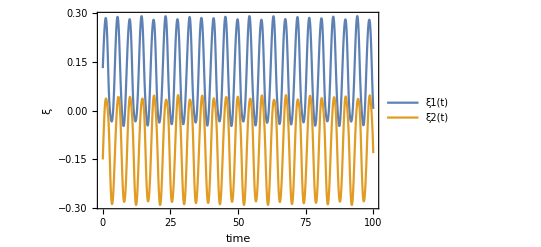

```mathematica
Plot[{Ξ1sol[t],Ξ2sol[t]},{t,0,tmax},Frame->True,FrameLabel->{"time","ξ"},PlotLegends->{"ξ1(t)","ξ2(t)"}]
```

TURN RATE TIME VARIATION

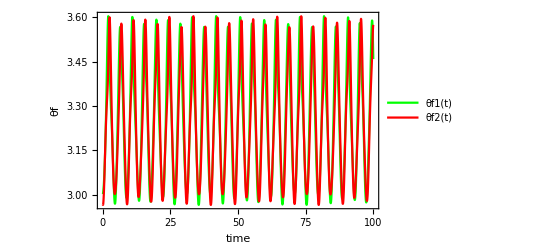

```mathematica
Plot[{Θ1sol[t],Θ2sol[t]},{t,0,tmax},Frame->True,FrameLabel->{"time","θf"},PlotLegends->{"θf1(t)","θf2(t)"},PlotStyle->{Green,Red}]
```

EVERYTHING TOGETHER

DISTANCE BETEWEEN 2 FISH TIME VARIATION

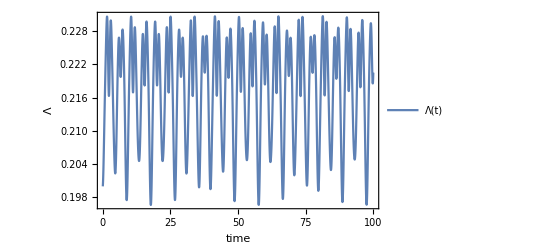

```mathematica
Plot[{Xsol[t]},{t,0,tmax},Frame->True,FrameLabel->{"time","Λ"},PlotLegends->{"Λ(t)"}]
```